# Analyze

Read path

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataPath=Import["path.txt","Table"];
```

```mathematica
pltPath=Show[
ListPointPlot3D[dataPath,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Black],
ListPointPlot3D[dataPath,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Black]/.Point->Line
]
```

-Graphics3D-

Read grid

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataSol=Import["solution.txt","Table"];
```

```mathematica
pltGrid=Show[ListPointPlot3D[dataSol,PlotRange->{{-0.05,1.05},{-0.05,1.05},{0,2}}],pltPath]
```

-Graphics3D-

```mathematica
Export["figures/grid.png",pltGrid,ImageResolution->150]
```

figures/grid.png

Interpolation functions

```mathematica
coeffs[p0_,p1_,p2_,p3_,x_]:=Module[
{a}
,
a=Association[];
a["0"]=-1/2*x^3+x^2-1/2*x;
a["1"]=3/2*x^3-5/2*x^2+1;
a["2"]=-3/2*x^3+2*x^2+1/2*x;
a["3"]=1/2*x^3-1/2*x^2;

Return[a];
];
```

```mathematica
fInterp[p0_,p1_,p2_,p3_,x_]:=Module[
{a}
,
a=coeffs[p0,p1,p2,p3,x];
Return[p0*a["0"]+p1*a["1"]+p2*a["2"]+p3*a["3"]];
];
```

```mathematica
fInterp2[x_,y_,delta_]:=Module[
{find,nbr4,xUnique,lines,qs,zInterp}
,
(* Try to find *)
find=Select[dataSol,#[[1]]==x&&#[[2]]==y&];
If[find≠{},Return[find[[1,3]]]];

(* Interpolate *)
nbr4=Select[dataSol,Abs[#[[1]]-x]≤2*delta&&Abs[#[[2]]-y]≤2*delta&];
xUnique=Sort[DeleteDuplicates[nbr4[[;;,1]]]];
lines=Table[Select[nbr4,#[[1]]==xUnique[[iLine]]&],{iLine,1,4}];
qs=Table[fInterp[lines[[iLine,1,3]],lines[[iLine,2,3]],lines[[iLine,3,3]],lines[[iLine,4,3]],(y-lines[[iLine,2,2]])/(lines[[iLine,3,2]]-lines[[iLine,2,2]])],{iLine,1,4}];
zInterp=fInterp[qs[[1]],qs[[2]],qs[[3]],qs[[4]],(x-xUnique[[2]])/(xUnique[[3]]-xUnique[[2]])];
Return[zInterp]
];
```

Test 1D interpolation

```mathematica
delta=0.05;
fakeData=Table[{(i-1)/20//N,RandomReal[{0,1}]},{i,21}];
```

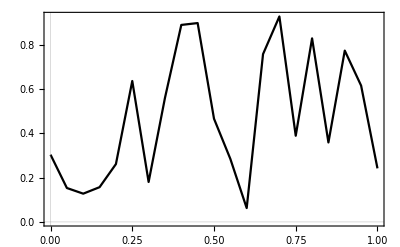

```mathematica
pltFake=ListLinePlot[fakeData,PlotStyle->Black]
```

```mathematica
gridEval=Table[x,{x,0.06,0.94,0.01}];
```

```mathematica
gridInterp={};
Do[
nbr4=Select[fakeData,Abs[#[[1]]-gridPt]≤2*delta&];
yInterp=fInterp[nbr4[[1,2]],nbr4[[2,2]],nbr4[[3,2]],nbr4[[4,2]],(gridPt-nbr4[[2,1]])/(nbr4[[3,1]]-nbr4[[2,1]])];
AppendTo[gridInterp,{gridPt,yInterp}];
,{gridPt,gridEval}];
```

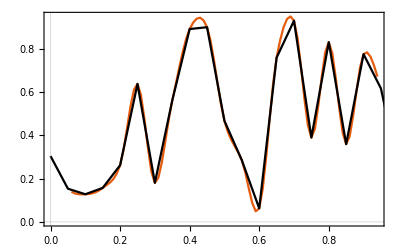

```mathematica
Show[ListLinePlot[gridInterp],pltFake]
```

2D interpolation

```mathematica
delta=0.025;
```

```mathematica
d=0.005;
gridInterp=Flatten[Table[{i,j},{i,delta+d,1-delta-d,d},{j,delta+d,1-delta-d,d}],1];
```

```mathematica
dataInterp={};
Monitor[
Do[
AppendTo[dataInterp,{gridInterp[[i,1]],gridInterp[[i,2]],fInterp2[gridInterp[[i,1]],gridInterp[[i,2]],delta]}]
,{i,1,Length[gridInterp]}];
,ProgressIndicator[i,{1,Length[gridInterp]}]]
```

```mathematica
pltInterp=ListPointPlot3D[dataInterp,PlotRange->{0,2}]
```

-Graphics3D-

```mathematica
pltTog=Show[pltInterp,pltPath]
```

-Graphics3D-

```mathematica
Export["figures/grid_resampled.png",pltTog,ImageResolution->150]
```

figures/grid_resampled.png

Plot only points along the graph

```mathematica
pathTest={};
radius=0.3;
nData=2000;
Do[
x=0.5+radius*i/nData*Cos[8*Pi*(i-1)/(nData-1)];
y=0.5+radius*i/nData*Sin[8*Pi*(i-1)/(nData-1)];
If[i≠nData,
z=Sin[8*Pi*(i-1)/(nData-1)]//N,
z=pathTest[[1,3]]
];
AppendTo[pathTest,{x,y,z}];
,{i,1,nData}];
```

```mathematica
pathInterp={};
Do[
AppendTo[pathInterp,{d[[1]],d[[2]],fInterp2[d[[1]],d[[2]],delta]}]
,{d,pathTest}];
```

```mathematica
pltTraj=Grid[{{ListPointPlot3D[pathInterp]/.Point->Line,ListPointPlot3D[dataPath,PlotStyle->Black]}}]
```

-Graphics3D- | -Graphics3D-

```mathematica
Export["figures/path_interp.png",pltTraj,ImageResolution->150]
```

figures/path_interp.png